```mathematica
(*算一下运动方程*)
(*上指标度规，下指标动量*)
ClearAll["Global`*"];
ClearAll[m];
m[r_]:=1-Qm^2/(2r)+(A Qm^4)/(40 r^5);
F01=-Qm(2a r Cos[θ])/((r^2+a^2 Cos[θ]^2)^2);
F02=-Qm((r^2-a^2 Cos[θ]^2)a Sin[θ])/((r^2+a^2 Cos[θ]^2)^2);
Fdown={{0,F01,F02,0},{-F01,0,0,F01 a Sin[θ]^2},{-F02,0,0,(r^2+a^2)/a F02},{0,-F01 a Sin[θ]^2,-(r^2+a^2)/a F02,0}};
Σ=r^2+a^2 Cos[θ]^2;
Δ=r^2-2 m[r]r+a^2;
gDown={{-(1-(2 m[r]r)/Σ),0,0,-(1/Σ)2 a m[r]r Sin[θ]^2},{0,Σ/Δ,0,0},{0,0,Σ,0},{-(1/Σ)2 a m[r]r Sin[θ]^2,0,0,(r^2+a^2+(1/Σ)2 m[r] a^2 r Sin[θ]^2)Sin[θ]^2}};
(*P形式的霍奇对偶*)
(*DualPup=-1/(Σ Sin[θ]){{0,(r^2+a^2)/a P02,-P01 a Sin[θ]^2,0},{-(r^2+a^2)/aP02,0,0,-P02},{P01 a Sin[θ]^2,0,0,P01},{0,P02,-P01,0}};
DualPdown=gDown.DualPup.gDown//Simplify;
sp=1/2(P01^2-P02^2/(a^2 Sin[θ]^2));
tp=(-P01 P02)/(a Sin[θ]);*)
(*Fdown=(1-A sp)Pdown-B tp DualPdown//Simplify;*)
gij={{(-((a^2+r^2)^2-a^2 (a^2-2 m[r]r+r^2) Sin[θ]^2))/((r^2+a^2 Cos[θ]^2)(a^2-2 m[r]r+r^2)),0,0,-(2 a m[r]r)/((r^2+a^2 Cos[θ]^2)(a^2-2 m[r]r+r^2))},{0,(a^2-2 m[r]r+r^2)/(r^2+a^2 Cos[θ]^2),0,0},{0,0,1/(r^2+a^2 Cos[θ]^2),0},{-(2 a m[r]r)/((r^2+a^2 Cos[θ]^2)(a^2-2 m[r]r+r^2)),0,0,((a^2-2 m[r]r+r^2)-a^2 Sin[θ]^2)/((r^2+a^2 Cos[θ]^2)(a^2-2 m[r]r+r^2)Sin[θ]^2)}};
(*保留至A的一阶,F=P
*)Xdown=Fdown.gij.Fdown//Simplify;
X=-1/2(F01^2-F02^2/(a^2 Sin[θ]^2))/.{t-> t[λ],r-> r[λ],θ-> θ[λ],ϕ-> ϕ[λ]}//Simplify;
Y=(F01 F02)/(a Sin[θ])/.{t-> t[λ],r-> r[λ],θ-> θ[λ],ϕ-> ϕ[λ]}//Simplify;
δ1=1/2 A X;
δ2=7/8(A Y^2)/X;
δ3=-((a^2 A Qm^2 (-A Qm^4+20 r^4 (a^2+Qm^2+(-2+r) r)) Cos[θ]^2 (126 a^10+840 a^8 r^2+2240 a^6 r^4+8448 a^4 r^6+4352 a^2 r^8+15360 r^10+2 a^2 (105 a^8+672 a^6 r^2+1680 a^4 r^4+5632 a^2 r^6+2176 r^8) Cos[2 θ]+8 a^4 (15 a^6+84 a^4 r^2+168 a^2 r^4+352 r^6) Cos[4 θ]+45 a^10 Cos[6 θ]+192 a^8 r^2 Cos[6 θ]+224 a^6 r^4 Cos[6 θ]+10 a^10 Cos[8 θ]+24 a^8 r^2 Cos[8 θ]+a^10 Cos[10 θ]))/(8 (A Qm^2-4 r^4) (A Qm^4-20 r^4 (a^2+Qm^2+(-2+r) r)) (a^2+2 r^2+a^2 Cos[2 θ])^6))/.{t-> t[λ],r-> r[λ],θ-> θ[λ],ϕ-> ϕ[λ]};
δ4=-((a^2 A Qm^4 Cos[θ]^2 (462 a^12+3780 a^10 r^2+13440 a^8 r^4+26240 a^6 r^6+31488 a^4 r^8+48640 a^2 r^10+12288 r^12+4 a^2 (198 a^10+1575 a^8 r^2+5376 a^6 r^4+9840 a^4 r^6+10496 a^2 r^8+12160 r^10) Cos[2 θ]+a^4 (495 a^8+3600 a^6 r^2+10752 a^4 r^4+15744 a^2 r^6+10496 r^8) Cos[4 θ]+220 a^12 Cos[6 θ]+1350 a^10 r^2 Cos[6 θ]+3072 a^8 r^4 Cos[6 θ]+2624 a^6 r^6 Cos[6 θ]+66 a^12 Cos[8 θ]+300 a^10 r^2 Cos[8 θ]+384 a^8 r^4 Cos[8 θ]+12 a^12 Cos[10 θ]+30 a^10 r^2 Cos[10 θ]+a^12 Cos[12 θ]))/(16 (-3 A Qm^4 r^2+4 Qm^2 r^6-2 a^2 A Qm^4 Cos[θ]^2) (a^2+2 r^2+a^2 Cos[2 θ])^6))/.{t-> t[λ],r-> r[λ],θ-> θ[λ],ϕ-> ϕ[λ]};
δ5=(a^2 A Qm^2 (-126 a^10 A Qm^4+4620 a^14 r^2-840 a^8 A Qm^4 r^2+44940 a^12 r^4+2520 a^10 Qm^2 r^4-2240 a^6 A Qm^4 r^4-5040 a^10 r^5+191520 a^10 r^6+16800 a^8 Qm^2 r^6-8448 a^4 A Qm^4 r^6-33600 a^8 r^7+458400 a^8 r^8+44800 a^6 Qm^2 r^8-4352 a^2 A Qm^4 r^8-89600 a^6 r^9+791040 a^6 r^10+168960 a^4 Qm^2 r^10-15360 A Qm^4 r^10-337920 a^4 r^11+1057280 a^4 r^12+87040 a^2 Qm^2 r^12-174080 a^2 r^13+1003520 a^2 r^14+307200 Qm^2 r^14-614400 r^15+430080 r^16+2 a^2 (3960 a^12 r^2+37560 a^10 r^4+240 a^4 r^4 (-7 A Qm^4+4 r^4 (35 Qm^2-70 r+576 r^2))+128 r^8 (-17 A Qm^4+20 r^4 (17 Qm^2+2 r (-17+56 r)))+512 a^2 r^6 (-11 A Qm^4+10 r^4 (22 Qm^2+r (-44+119 r)))-96 a^6 (7 A Qm^4 r^2-20 r^6 (7 Qm^2+r (-14+183 r)))-105 a^8 (A Qm^4-4 r^4 (5 Qm^2+2 r (-5+184 r)))) Cos[2 θ]+2 a^4 (2475 a^10 r^2+21675 a^8 r^4+96 a^2 r^4 (-7 A Qm^4+20 r^4 (7 Qm^2+2 r (-7+45 r)))+128 r^6 (-11 A Qm^4+10 r^4 (22 Qm^2+r (-44+63 r)))-48 a^4 (7 A Qm^4 r^2-20 r^6 (7 Qm^2+r (-14+159 r)))-60 a^6 (A Qm^4-4 r^4 (5 Qm^2+2 r (-5+166 r)))) Cos[4 θ]-45 a^10 A Qm^4 Cos[6 θ]+2200 a^14 r^2 Cos[6 θ]-192 a^8 A Qm^4 r^2 Cos[6 θ]+16600 a^12 r^4 Cos[6 θ]+900 a^10 Qm^2 r^4 Cos[6 θ]-224 a^6 A Qm^4 r^4 Cos[6 θ]-1800 a^10 r^5 Cos[6 θ]+48960 a^10 r^6 Cos[6 θ]+3840 a^8 Qm^2 r^6 Cos[6 θ]-7680 a^8 r^7 Cos[6 θ]+65280 a^8 r^8 Cos[6 θ]+4480 a^6 Qm^2 r^8 Cos[6 θ]-8960 a^6 r^9 Cos[6 θ]+30720 a^6 r^10 Cos[6 θ]-10 a^10 A Qm^4 Cos[8 θ]+660 a^14 r^2 Cos[8 θ]-24 a^8 A Qm^4 r^2 Cos[8 θ]+3860 a^12 r^4 Cos[8 θ]+200 a^10 Qm^2 r^4 Cos[8 θ]-400 a^10 r^5 Cos[8 θ]+7520 a^10 r^6 Cos[8 θ]+480 a^8 Qm^2 r^6 Cos[8 θ]-960 a^8 r^7 Cos[8 θ]+4320 a^8 r^8 Cos[8 θ]-a^10 A Qm^4 Cos[10 θ]+120 a^14 r^2 Cos[10 θ]+440 a^12 r^4 Cos[10 θ]+20 a^10 Qm^2 r^4 Cos[10 θ]-40 a^10 r^5 Cos[10 θ]+320 a^10 r^6 Cos[10 θ]+10 a^14 r^2 Cos[12 θ]+10 a^12 r^4 Cos[12 θ]) Csc[θ]^2 Sin[2 θ]^2)/(32 (a^2+2 r^2+a^2 Cos[2 θ])^6 (-A^2 Qm^6-80 r^8 (2 a^2+Qm^2+2 (-1+r) r)+4 A Qm^2 r^2 (5 a^4+25 a^2 r^2+2 r^2 (3 Qm^2+5 r (-1+2 r)))+20 a^2 A Qm^2 r^2 (a^2+r^2) Cos[2 θ]))/.{t-> t[λ],r-> r[λ],θ-> θ[λ],ϕ-> ϕ[λ]};
(*Print[Xup[[2,3]]];
Print[Xup[[3,2]]];*)
QQ={qt,qr,qθ,qϕ};
Gdown=gDown+k Xdown;
Ginverse=Inverse[Gdown];
(*Print[Gdown[[2,3]]];
Print[Ginverse[[3,2]]];*)
H=1/2(Sum[Ginverse[[i,j]]QQ[[i]]QQ[[j]],{i,1,4},{j,1,4}]);
du={td,rd,θd,ϕd,qrd,qθd};
td=D[H,qt];
rd=D[H,qr];
θd=D[H,qθ];
ϕd=D[H,qϕ];
qrd=-D[H,r];
qθd=-D[H,θ];
Deom=du/.{qt->-EE,qϕ-> LL,t-> t[λ],r-> r[λ],θ-> θ[λ],ϕ-> ϕ[λ],qr-> qr[λ],qθ-> qθ[λ]};
Print[X];
Print["-------------------------------Done 1-------------------------------------------"]
```

(Qm^2 (a^4 Cos[θ[λ]]^4-6 a^2 Cos[θ[λ]]^2 r[λ]^2+r[λ]^4))/(2 (a^2 Cos[θ[λ]]^2+r[λ]^2)^4)

-------------------------------Done 1-------------------------------------------

```mathematica
(*定义Kerr度规*)
ClearAll[MetricDown];
MetricDown[a_][{t_,r_,θ_,ϕ_}]:=Module[{tt,rr,θθ,ϕϕ,tϕ,Σ,Δ},
Σ=r^2+a^2 Cos[θ]^2;
Δ=r^2-2m[r] r+a^2;
tt=-(1-(2 m[r]r)/Σ);
rr=Σ/Δ;
θθ=Σ;
ϕϕ=(r^2+a^2+(1/Σ)2 m[r] a^2 r Sin[θ]^2)Sin[θ]^2;
tϕ=-(1/Σ)2 a m[r]r Sin[θ]^2;
({{tt, 0, 0, tϕ}, {0, rr, 0, 0}, {0, 0, θθ, 0}, {tϕ, 0, 0, ϕϕ}})];
(*把θ变到0~π，把ψ变到0~2π*)
ClearAll[WrapAngle];
WrapAngle[a1_,a2_]:=Module[{x1=a1,x2=a2},
While[x1>π,x1=x1-2π];
While[x1<-π,x1=x1+2π];
If[x1<0,x1=-x1;x2=x2+π];
While[x2≥2π,x2=x2-2π];
While[x2<0,x2=x2+2π];
{x1,x2}];
(*ZAMO标架场*)
ClearAll[LocalTetrads];
LocalTetrads[pos_,metric_]:=Module[{e0,e1,e2,e3,gtt,grr,gθθ,gϕϕ,gtϕ},
{gtt,grr,gθθ,gϕϕ,gtϕ}=Extract[metric,{{1,1},{2,2},{3,3},{4,4},{1,4}}];
e0=√(-(gϕϕ/(gtt gϕϕ-gtϕ gtϕ))){1,0,0,-(gtϕ/gϕϕ)};(*Subscript[e, t]*)
e1={0,-(1/(√grr)),0,0};(*Subscript[e, r]*)
e2={0,0,1/(√gθθ),0};(*Subscript[e, θ]*)
e3={0,0,0,-(1/(√gϕϕ))};(*Subscript[e, ϕ]*)
{e0,e1,e2,e3}];
(*得到光线的初始方向以及相对应的上标四速度*)
ClearAll[GetRayDirection];
GetRayDirection[a0_,metric_,pos_,fov_,npix_][i_,j_]:=Module[{λdot,xscr,yscr,θx,ψx,vel,e0,e1,e2,e3,κ},
{xscr,yscr}=(2Tan[fov/2]/npix)(#-(1/2)(npix+1))&/@{i,j};
{θx,ψx}=WrapAngle[2ArcTan[(1/2)(√(xscr^2+yscr^2))],ArcTan[-yscr,-xscr]];
vel=N@{Cos[θx],Sin[θx]Cos[ψx],Sin[θx]Sin[ψx]};
{e0,e1,e2,e3}=N@LocalTetrads[pos,metric];
{gtt,grr,gθθ,gϕϕ,gtϕ}=Extract[metric,{{1,1},{2,2},{3,3},{4,4},{1,4}}];
{Xtt,Xrr,Xθθ,Xϕϕ,Xtϕ}=Extract[Xdown,{{1,1},{2,2},{3,3},{4,4},{1,4}}];
{C3,C2,C1}={(Xrr Cos[θx]^2)/grr+(Sin[θx]^2 (gϕϕ Xθθ Cos[ψx]^2+gθθ Xϕϕ Sin[ψx]^2))/(gθθ gϕϕ),(2 √(gϕϕ/(gtϕ^2-gtt gϕϕ)) (gϕϕ Xtϕ-gtϕ Xϕϕ) Sin[θx] Sin[ψx])/gϕϕ^(3/2),(gϕϕ^2 Xtt-2 gtϕ gϕϕ Xtϕ+gtϕ^2 Xϕϕ)/(gtϕ^2 gϕϕ-gtt gϕϕ^2)}/.{a->a0,t-> pos[[1]],r->pos[[2]],θ-> pos[[3]],ϕ->pos[[4]]};
κ=(-k C2-√(k^2 C2^2+4(k C3+1)(1-k C1)))/(2(k C1-1));
λdot=-κ e0+vel[[1]]e1+vel[[2]]e2+vel[[3]]e3;
λdot];
(*数值求解单条光线的方程*)
ClearAll[TraceSingleRay];
TraceSingleRay[a0_,pos_,fov_,npix_][i_,j_]:=Module[{λF=3000,metric,horizon,λdot,eqns,E0,L0,idata,initialConditions,sol,frame,momentum,eom,delta1,delta2,delta3,delta4,delta5,data},
horizon=Max[r/.NSolve[r^6-2m[r] r^5+r^4 a0^2==0,r,Reals]];
metric=Gdown/.{a->a0,t-> pos[[1]],r->pos[[2]],θ-> pos[[3]],ϕ->pos[[4]]};
λdot=GetRayDirection[a0,MetricDown[a0][pos],pos,fov,npix][i,j];
momentum=metric.λdot;
{E0,L0}={-momentum[[1]],momentum[[4]]};
idata=Join[pos,{momentum[[2]],momentum[[3]]}];
initialConditions=Thread[{t[0],r[0],θ[0],ϕ[0],qr[0],qθ[0]}==idata];
eom=Thread[{t'[λ],r'[λ],θ'[λ],ϕ'[λ],qr'[λ],qθ'[λ]}==Deom];
eqns=N[Join[eom,initialConditions]/.{a->a0,EE-> E0,LL-> L0}];
{sol,data}=Reap[NDSolve[eqns,{t,r,θ,ϕ,qr,qθ},{λ,0,λF},Method->{"EventLocator", "Event"->{r[λ]-1.01horizon,r[λ]-100000horizon},"EventAction":>{Throw[λF =λ,"StopIntegration"],Throw[λF =λ,"StopIntegration"]}},EvaluationMonitor:>(Sow[Evaluate[Abs[δ1/.{a->a0}]],del1];Sow[Evaluate[Abs[δ2/.{a->a0}]],del2];Sow[Evaluate[Abs[δ3/.{a->a0}]],del3];Sow[Evaluate[Abs[δ4/.{a->a0}]],del4];Sow[Evaluate[Abs[δ5/.{a->a0}]],del5])]];
delta1=Max[data[[1]]];
delta2=Max[data[[2]]];
delta3=Max[data[[3]]];
delta4=Max[data[[4]]];
delta5=Max[data[[5]]];
{r[λF],θ[λF],ϕ[λF],qr[λF],qθ[λF],E0,L0,delta1,delta2,delta3,delta4,delta5}/.sol[[1]]];
(*搞一个进度条查看跑了多少*)
ClearAll[MonitorParallelTable];
MonitorParallelTable[expr_,npix_]:= Module[{res,iterCount=npix^2,progress=0},
  SetSharedVariable[progress];
  res=Monitor[ParallelTable[(progress++;expr[j,i]),{i,1,npix},{j,1,npix}],
    Column[{ToString@progress<>" of "<>ToString@iterCount,ProgressIndicator[progress,{0,iterCount}]},Alignment->Center]];
  UnsetShared[progress];
res];
(*跑所有的点*)
ClearAll[TraceRay];
TraceRay[a_,pos_,fov_,npix_]:=MonitorParallelTable[TraceSingleRay[a,pos,fov,npix],npix];
Print["-------------------------------Done 2-------------------------------------------"]
```

-------------------------------Done 2-------------------------------------------

```mathematica
(*准备就绪，开始跑函数*)
ClearAll[result,resultplot]
a0=0;
Qm=0.7;
A=5.08;
k=3.5 A;
horizon0=Max[r/.NSolve[r^6-2m[r] r^5+r^4 a0^2==0,r,Reals]];
pos={0,80,π/2-0.01,0};
fov=π/5;
npix=128;(*should be even*)
result={TraceRay[a0,pos,fov,npix]};
resultplot={result[[1]][[All,All,1;;3]]};
(*验证一下末态哈密顿量*)
icheck=64;(*检查点(icheck,icheck)的哈密顿量是否为0*)
Print[H/.{r->result[[1]][[icheck,icheck,1]],θ->result[[1]][[icheck,icheck,2]],qr->result[[1]][[icheck,icheck,4]],qθ->result[[1]][[icheck,icheck,5]],qt->-result[[1]][[icheck,icheck,6]],qϕ-> result[[1]][[icheck,icheck,7]],a-> a0}];
Print[ Max[result[[1]][[All,All,8]]]];
Print[ Max[result[[1]][[All,All,9]]]];
Print[ Max[result[[1]][[All,All,10]]]];
Print[ Max[result[[1]][[All,All,11]]]];
Print[ Max[result[[1]][[All,All,12]]]]
```

0.0000624586

0.0686264

0.

0.

0.

«1 more identical outputs»

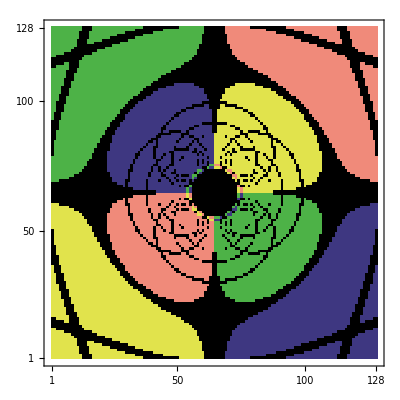

```mathematica
split=π/18;
ClearAll[GetColor];
ClearAll[GetClosestAngle];
{θ0,ϕ0}={pos[[3]],pos[[4]]};
GetClosestAngle[x_]:=With[{q=IntegerPart[x/split]},Min[(q+1)split-x,x-q split]];
GetColor[{rF_,θFx_,ϕFx_}]:=Module[{θF,ϕF},
If[rF<1.02 horizon0,Return[Black]];
{θF,ϕF}={θFx,ϕFx};
{n1,n2}={Sin[θF] Sin[ϕF-ϕ0],-Cos[θ0]Sin[θF] Cos[ϕF-ϕ0]+Sin[θ0]Cos[θF]};
(*n3=Sin[θ0]Sin[θF] Cos[ϕF-ϕ0]+Cos[θ0]Cos[θF];*)
(*psi=ArcCos[(Cos[θF] Cos[θ0]+Sin[θ0] Cos[ϕ0-ϕF] Sin[θF])/(Sqrt[(Cos[θ0] (Cos[θF] Cos[θ0]+Sin[θ0] Cos[ϕ0-ϕF] Sin[θF]))^2+(Sin[θ0] (Cos[θF] Cos[θ0]+ Sin[θ0] Cos[ϕ0-ϕF] Sin[θF]))^2+(Sin[θF] Sin[ϕ0-ϕF])^2])];*)
{theta,psi}=WrapAngle[ArcSin[n2],ArcSin[n1]];
Which[GetClosestAngle[theta]≤0.01||GetClosestAngle[psi]≤0.01,Return[Black],n1>0&&n2>0,RGBColor[{240,138,122}/255](*red*),n1>0&&n2<0,RGBColor[{62,55,129}/255](*blue*),n1<0&&n2< 0,RGBColor[{225,227,76}/255](*yellow*),n1<0&&n2>0,RGBColor[{77,178,71}/255](*green*)]];
MatrixPlot[Map[GetColor,resultplot[[1]],{2}],DataReversed->{True,False},AspectRatio->1]
```

```mathematica
(*画Shadow*)
MatrixPlot[Map[If[#<1.02horizon0,1,0]&,resultplot[[1]]⟦All,All,1⟧,{2}],ColorFunction->"Monochrome",DataReversed->{True,False},AspectRatio->1]
```

-Graphics-